```mathematica
Practical 1 ;
ComplexExpand[z/.N[Solve[z^8-1==0]]]
```

{0.-1. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,0.+1. ⅈ,0.707107-0.707107 ⅈ,-0.707107+0.707107 ⅈ,0.707107+0.707107 ⅈ,-0.707107-0.707107 ⅈ}

```mathematica
A1= Show[Graphics[{Thick,Blue,Circle[{0,0},1]}],
ListLinePlot[{{1,0},{0.707107,0.707107},{0,1},{-0.707107,0.707107},{-1,0},{-0.707107,-0.707107},{0,-1},{0.707107,-0.707107},{1,0}},PlotStyle->Purple,PlotMarkers->Automatic],Axes-> True,ImageSize-> 100, PlotLabel-> "For n=8"]
```

-Graphics-

```mathematica
Practical 2 (finding all the solutions of the eqn;
```

{5 Cos[π/8]-5 ⅈ Sin[π/8],-5 Cos[π/8]+5 ⅈ Sin[π/8],5 ⅈ Cos[π/8]+5 Sin[π/8],-5 ⅈ Cos[π/8]-5 Sin[π/8]}

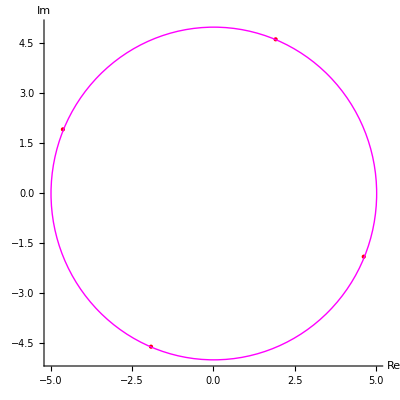

```mathematica
pts=ComplexExpand[z/.Solve[z^4+625*I==0]]
abc={Re[#],Im[#]}&/@pts;
a=Graphics[{Red,PointSize[Large],Point[abc]},Axes-> True,AxesLabel-> {"Re","Im"}];
b=Graphics[{Thick,Magenta,Circle[{0,0},5]}];
Show[a,b]
```

```mathematica
Practical 3 parametric of ellipse for rotation and shifting;
```

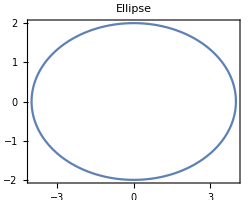

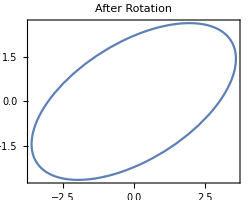

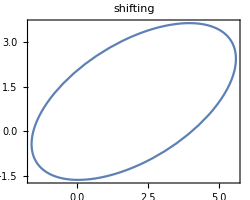

```mathematica
A1=ParametricPlot[{4Cos[t],2Sin[t]},{t,0,2π},Frame-> True,ImageSize-> 250,PlotLabel-> "Ellipse"]
A2=ParametricPlot[{4Cos[t] Cos[π/6]-2Sin[t] Sin[π/6],4Cos[t] Sin[π/6]+2Sin[t] Cos[π/6]},{t,0,2π},Frame->True,ImageSize->250,PlotLabel->"After Rotation"]
A3=ParametricPlot[{4Cos[t] Cos[π/6]-2Sin[t] Sin[π/6]+2,4Cos[t] Sin[π/6]+2Sin[t] Cos[π/6]+1},{t,0,2π},Frame->True,ImageSize->250,PlotLabel->"shifting"]
```

```mathematica
Practical 5  image of right half plane Re z >1 ;
```

```mathematica
Solve[Subscript[w, 1]==(-1+I)Subscript[z, 1]-2+3 I,Subscript[z, 1]]
```

{{z_1→1/2 (-5+ⅈ (1-w_1)-w_1)}}

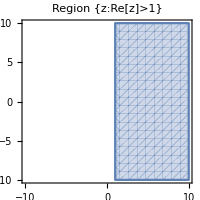
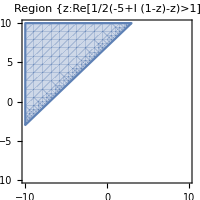

```mathematica
Subscript[z, 1]=x+ I y;
A1=RegionPlot[Re[Subscript[z, 1]]>1,{x,-10,10},{y,-10,10},Axes-> True,ImageSize->200,PlotLabel->"Region {z:Re[z]>1}"];
A2=RegionPlot[Re[1/2(-5+I (1-Subscript[z, 1])-Subscript[z, 1])]>1,{x,-10,10},{y,-10,10},Axes-> True,ImageSize->200,PlotLabel->"Region {z:Re[1/2(-5+I (1-z)-z)>1]"];
Print[A1,A2]
```

```mathematica
Practical 6  image of right half plane A={z:Rez≥ 1/2};
```

```mathematica
Solve[Subscript[w, 2]==1/Subscript[z, 2],Subscript[z, 2]]
```

{{z_2→1/w_2}}

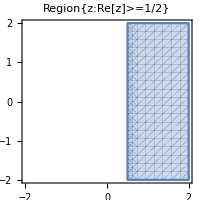
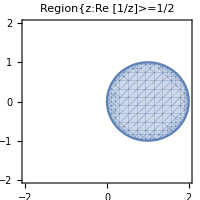

```mathematica
z=x+I y;
A1=RegionPlot[Re[z]≥ 1/2,{x,-2,2},{y,-2,2},Axes-> True,ImageSize->200,PlotLabel->"Region{z:Re[z]>=1/2}"];
A2=RegionPlot[Re[1/z]≥ 1/2,{x,-2,2},{y,-2,2},Axes-> True, ImageSize-> 200,PlotLabel->"Region{z:Re [1/z]>=1/2"];
Print[A1,A2]
```

```mathematica
Practical 7 plot of vertical lines and horizontal lines ;
```

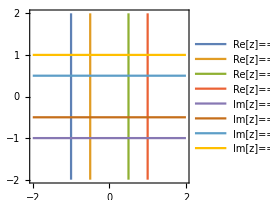
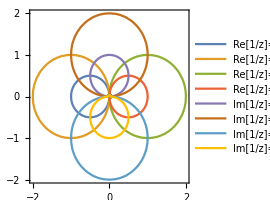

```mathematica
z=x+I y;
A1=ContourPlot[{Re[z]==-1,Re[z]==-1/2,Re[z]==1/2,Re[z]==1,Im[z]==-1,Im[z]==-1/2,Im[z]==1/2,Im[z]==1},{x,-2,2},{y,-2,2},Axes-> True,ImageSize->200,PlotLegends->{"Re[z]==-1","Re[z]==-1/2","Re[z]==1/2","Re[z]==1","Im[z]==-1","Im[z]==-1/2","Im[z]==1/2","Im[z]==1"}];
A2=ContourPlot[{Re[1/z]==-1,Re[1/z]==-1/2,Re[1/z]==1/2,Re[1/z]==1,Im[1/z]==-1,Im[1/z]==-1/2,Im[1/z]==1/2,Im[1/z]==1},{x,-2,2},{y,-2,2},Axes-> True,ImageSize->200,PlotLegends->{"Re[1/z]==-1","Re[1/z]==-1/2","Re[1/z]==1/2","Re[1/z]==1","Im[1/z]==-1","Im[1/z]==-1/2","Im[1/z]==1/2","Im[1/z]==1"}];
Print[A1,A2]
```

```mathematica
Practical 8   polygonal path c=c1+c2+c3;
```

The parametrization of C1,C2,C3 are given by

C1:z1(t)=(-1+ⅈ) (1-t)-t,0≤t≤1

C2:z2(t)=-1+(2+ⅈ) t,0≤t≤1

C3:z3(t)=(1+ⅈ) (1-t)+(3-ⅈ) t,0≤t≤1

The plot of the polynomial path C is given by the figure

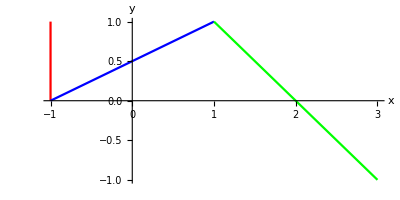

```mathematica
w1:=-1+I;
w2:=-1;
w3:=1+I;
w4:=3-I;
z1[t_]:=(1-t)w1+t w2;
z2[t_]:=(1-t)w2+t w3;
z3[t_]:=(1-t)w3+t w4;
Print["The parametrization of C1,C2,C3 are given by"];
Print["C1:z1(t)=",z1[t],",0≤t≤1"];
Print["C2:z2(t)=",z2[t],",0≤t≤1"];
Print["C3:z3(t)=",z3[t],",0≤t≤1"];
Print["The plot of the polynomial path C is given by the figure"]
ParametricPlot[{{Re[z1[t]],Im[z1[t]]},{Re[z2[t]],Im[z2[t]]},{Re[z3[t]],Im[z3[t]]}},{t,0,1},PlotStyle->{Red,Blue,Green},AxesLabel->{x,y}]
```

```mathematica
Practcial 9 line segment joing L from A to B;
```

```mathematica
Quit[];
```

The parametrization of line segment L is given by

L:z(t)=(2+(ⅈ π)/4) t0≤t≤1

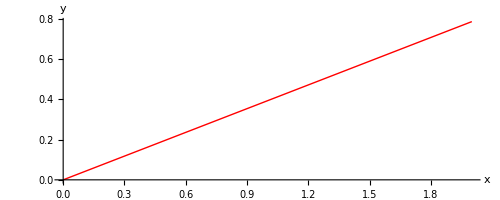

∫_L e^zⅆz=-1+((1+ⅈ) ⅇ^2)/(√2)

```mathematica
w1:=0;
w2:=2+I  π/4 ;
z[t_]:= (1-t)w1+t w2;
Print["The parametrization of line segment L is given by"];
Print["L:z(t)=",z[t],"0≤t≤1"];
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},PlotStyle-> {Thick,Red},AxesLabel->{x,y}]
f[z_]:= Exp[z];
Print["∫_L e^zⅆz=",ComplexExpand[Integrate[f[z[t]]z'[t],{t,0,1}]]]
```

```mathematica
Practical 10  upper semicircle oriented positively;
```

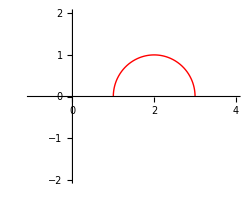

```mathematica
ParametricPlot[{2+Cos[t],Sin[t]},{t,0,π},PlotRange->{{-1,4},{-2,2}},PlotStyle->{Red,Thick},ImageSize-> 250]
```

```mathematica
f[z_]:=1/(z-2);
z[t_]:= 2+Cos[t]+ I Sin[t];
Print["∫_c 1/(z - 2)ⅆz=",ComplexExpand[Integrate[f[z[t]]z'[t],{t,0,π}]]]
```

∫_c 1/(z - 2)ⅆz=ⅈ π

```mathematica
Practical 11 integral c1= integral c2 = 4+2i ;
```

The parametrization of the line segment C_1is given by

C_1:z(t)=(-1-ⅈ) (1-t)+(3+ⅈ) t0≤t≤1

The parametrization of the portion of the parabola C_2 is given by

C_2:z(t)=(2+ⅈ) t+t^2-1≤t≤1

the plots of the line segment C_1and the portion of the parabola C_2 are given by the figure

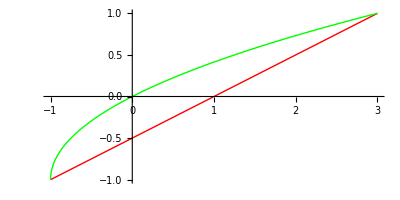

∫_C_1 zⅆz =4+2 ⅈ

∫_C_2 zⅆz =4+2 ⅈ

```mathematica
w1:=-1-I;
w2:=3+I;
z1[t_]:= (1-t)w1+t w2;
z2[t_]:=(t^2+2t)+I t;
Print["The parametrization of the line segment C_1is given by"];
Print["C_1:z(t)=",z1[t],"0≤t≤1"];
Print["The parametrization of the portion of the parabola C_2 is given by"];
Print["C_2:z(t)=",z2[t],"-1≤t≤1"];
Print["the plots of the line segment C_1and the portion of the parabola C_2 are given by the figure"]
Show[ParametricPlot[{Re[z1[t]],Im[z1[t]]},{t,0,1},PlotStyle-> {Thick,Red}],ParametricPlot[{Re[z2[t]],Im[z2[t]]},{t,-1,1},PlotStyle-> {Thick,Green}]]
f[z_]:=z;
Print["∫_C_1 zⅆz =",Integrate[f[z1[t]]z1'[t],{t,0,1}]];
Print["∫_C_2 zⅆz =",Integrate[f[z2[t]]z2'[t],{t,-1,1}]];
```

```mathematica
Practical 13 laurent series ;
```

```mathematica
Grid[Table[{n,Normal[Series[3/(2+z-z^2),{z,n,10}]]},{n,{0,2,Infinity}}],Frame->All]
```

0 | 3/2-(3 z)/4+(9 z^2)/8-(15 z^3)/16+(33 z^4)/32-(63 z^5)/64+(129 z^6)/128-(255 z^7)/256+(513 z^8)/512-(1023 z^9)/1024+(2049 z^10)/2048
2 | 1/3+(2-z)/9-1/(-2+z)+1/27 (-2+z)^2-1/81 (-2+z)^3+1/243 (-2+z)^4-1/729 (-2+z)^5+(-2+z)^6/2187-(-2+z)^7/6561+(-2+z)^8/19683-(-2+z)^9/59049+(-2+z)^10/177147
∞ | -513/z^10-255/z^9-129/z^8-63/z^7-33/z^6-15/z^5-9/z^4-3/z^3-3/z^2

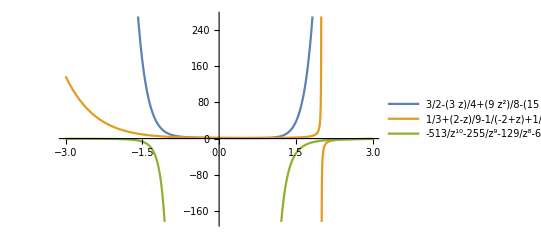

```mathematica
Plot[Evaluate[Table[{Normal[Series[3/(2+z-z^2),{z,n,10}]]},{n,{0,2,Infinity}}]],{z,-3,3},PlotLegends->"Expressions"]
```

```mathematica
Practical 14 locate the poles;
```

```mathematica
f[z_]:= 1/(5 z^4+26 z^2+5);
Print["f[z]=",f[z]];
Print[Denominator[f[z]]==0];
Solset=Sort[Solve[Denominator[f[z]]==0,z]];
Print[Solset];
Print["The singularities are"];
z1=ReplaceAll[z,Solset[[1]]];
Print["z1=",z1];
z2=ReplaceAll[z,Solset[[2]]];
Print["z2=",z2];
z3=ReplaceAll[z,Solset[[3]]];
Print["z3=",z3];
z4=ReplaceAll[z,Solset[[4]]];
Print["z4=",z4];
```

f[z]=1/(5+26 z^2+5 z^4)

5+26 z^2+5 z^4==0

{{z→-ⅈ/(√5)},{z→ⅈ/(√5)},{z→-ⅈ √5},{z→ⅈ √5}}

The singularities are

z1=-ⅈ/(√5)

z2=ⅈ/(√5)

z3=-ⅈ √5

z4=ⅈ √5

```mathematica
Practical 15 locate zeroes and poles  and justify residue;
```

```mathematica
g[z_]:=(π*Cot[π*z])/z^2;
Print["The zeroes are;",Reduce[g[z]==0,z]]
```

The zeroes are;C[1]∈ℤ&&z≠0&&z==(π/2+π C[1])/π

```mathematica
Poles=Solve[Denominator[g[z]]==0,z]
```

{{z→0},{z→0}}

```mathematica
residue=Residue[g[z],{z,0}]
```

-π^2/3

```mathematica
Practical 16 evaluate integral and then evalaute another one;
```

```mathematica
f[z_]:=Exp[2/z];
residue= SeriesCoefficient[f[z],{z,0,-1}];
Print["The residue of f[z] at the point z=0 is ", residue," ."]
integral=2Pi I*(residue);
Print["The value of ∫_(C_1^*) e^(2/z)ⅆz, by the cauchy residue theorem is: ",integral," ."]
```

The residue of f[z] at the point z=0 is 2 .

The value of ∫_(C_1^*) e^(2/z)ⅆz, by the cauchy residue theorem is: 4 ⅈ π .

```mathematica
g[z_]=1/(z^4+z^3-2 z^2);
Apart[g[z]]
```

1/(3 (-1+z))-1/(2 z^2)-1/(4 z)-1/(12 (2+z))

```mathematica
Subscript[residue, 0]=SeriesCoefficient[g[z],{z,0,-1}];
Subscript[residue, 1]=SeriesCoefficient[g[z],{z,1,-1}];
Subscript[residue, -2]=SeriesCoefficient[g[z],{z,-2,-1}];
Print["Residue of g[z] at z_0 = 0 is ", Subscript[residue, 0],", at z_1=1 is ",Subscript[residue, 1]," and at z_2=-2 is ",Subscript[residue, -2]," ."]
integral =2 Pi I*(Subscript[residue, 0]+Subscript[residue, 1]+Subscript[residue, -2]);
Print["The value of ∫_(C_1^*) 1/z^4ⅆz by cauchy residue theorem is : ",integral]
```

Residue of g[z] at z_0 = 0 is -1/4, at z_1=1 is 1/3 and at z_2=-2 is -1/12 .

The value of ∫_(C_1^*) 1/z^4ⅆz by cauchy residue theorem is : 0

```mathematica
Practical 12 ML inequality
```

The parametrization equation of the given curve is C : z[t] = 2+ⅈ t Where 0<t⩽1, which represent straight line joining the points z_0 = 2 and z_1 = 2+ⅈ.

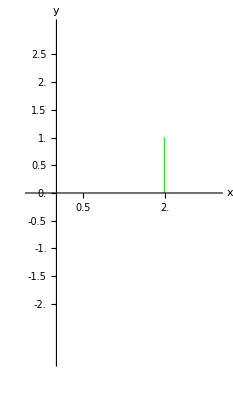

Length of the Arc is, L = 1 and the value of M is 1/5.

Using the ML Inequality, we have an upper bound for the given integral as 1/5.

```mathematica
z0=2;
z1=2+I;
z[t_]=z0+t*(z1-z0);
Print["The parametrization equation of the given curve is C : z[t] = ",ComplexExpand[z[t]]," Where 0<t⩽1, which represent straight line joining the points z_0 = ",z0," and z_1 = ",z1,"."]
p1=ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},AxesStyle->Arrowheads[{-0.03,0.03}],AxesLabel->{"x","y"},PlotStyle->{Thick,Green},AxesOrigin->{0,0},Ticks->{Range[-1,3,.5],Range[-2,2.5,0.5]},PlotRange->{{-0.5,3},{-3,3}}];
Show[p1]
L=Integrate[Abs[z'[t]],{t,0,1}];
f[z_]=1/(z^2+1);
r=ComplexExpand[Re[f[z[t]]]];
i=ComplexExpand[Im[f[z[t]]]];
M=Maximize[{(r^2+i^2)^(1/2),0⩽t⩽1},t];
ML=M[[1]]*L;
Print["Length of the Arc is, L = ",1," and the value of M is ", M[[1]],"."]
Print["Using the ML Inequality, we have an upper bound for the given integral as", ML,"."]
Manipulate[Show[ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},PlotStyle->{Thick,Red},PlotRange->2],ListLinePlot[{{{0,1},{Re[z[t]],Im[z[t]]}},{{0,-1},{Re[z[t]],Im[z[t]]}}},AxesOrigin->{0,0}]],{t,0,1}]
```

```mathematica
Practical 4 image of open disk under the mapping ;
```

```mathematica
Solve[Subscript[w, 1]==(3-4 I)Subscript[z, 1]+(6+2 I),Subscript[z, 1]]
```

{{z_1→1/25 (-10+3 w_1+2 ⅈ (-15+2 w_1))}}

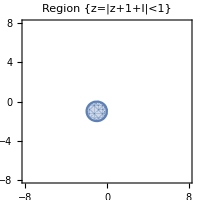
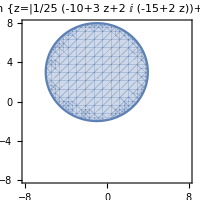

```mathematica
z=x+I y;
A1=RegionPlot[Abs[z+(1+I)]<1,{x,-8,8},{y,-8,8},Axes->True,ImageSize->200,PlotLabel->"Region {z=|z+1+I|<1}"];
A2=RegionPlot[Abs[1/25 (-10+3 z+2 ⅈ (-15+2 z))+(1+I)]<1,{x,-8,8},{y,-8,8},Axes->True,ImageSize->200,PlotLabel->"Region {z=|1/25 (-10+3 z+2 ⅈ (-15+2 z))+1+I|<1}"];
Print[A1,A2]
```